## Histogram

```mathematica
histodata=Import[NotebookDirectory[]<>"../data/"<>"Table_Stochastic_Resistance_CycleLength_50years.txt","CSV"];
```

```mathematica
histosorted=GatherBy[histodata⟦2;;,{2,3,4,5,6,7,8,9,10,1}⟧,Last];
```

```mathematica
histodata2=Import[NotebookDirectory[]<>"../data/"<>"Table_Stochastic_Resistance_Mono_Mix_50years.txt","CSV"];
```

```mathematica
histosorted2=GatherBy[histodata2⟦2;;,{2,3,4,5,6,7,8,9,10,1}⟧,Last];
```

#### Without tillage

```mathematica
histosorted⟦1,All,7⟧= histosorted⟦1,All,7⟧-histosorted⟦1,All,9⟧;
```

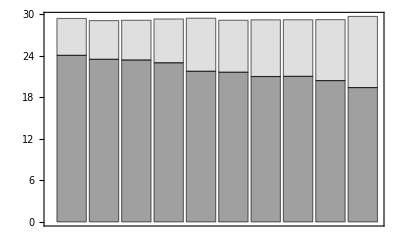

```mathematica
BarChart[histosorted⟦1,All,{9,7}⟧*100,ChartLayout->"Stacked", ChartStyle->{Directive[EdgeForm[{Thickness[Medium],Black}], Gray,Opacity[0.75]],Directive[EdgeForm[{Thickness[Medium],Black}], Gray,Opacity[0.25]]},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]]]
```

```mathematica
histosorted2⟦1,All,7⟧= histosorted2⟦1,All,7⟧-histosorted2⟦1,All,9⟧;
```

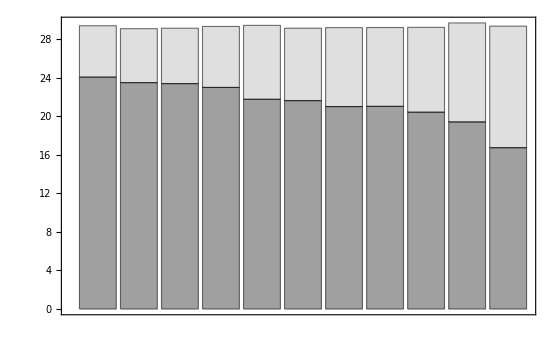

```mathematica
BarChart[Append[histosorted⟦1,All,{9,7}⟧*100, histosorted2⟦1,2,{9,7}⟧*100],ChartLayout->"Stacked", ChartStyle->{Directive[EdgeForm[{Thickness[Medium],Black}], Gray,Opacity[0.75]],Directive[EdgeForm[{Thickness[Medium],Black}], Gray,Opacity[0.25]]},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]]]
```

#### With tillage

```mathematica
histosorted⟦2,All,7⟧= histosorted⟦2,All,7⟧-histosorted⟦2,All,9⟧;
```

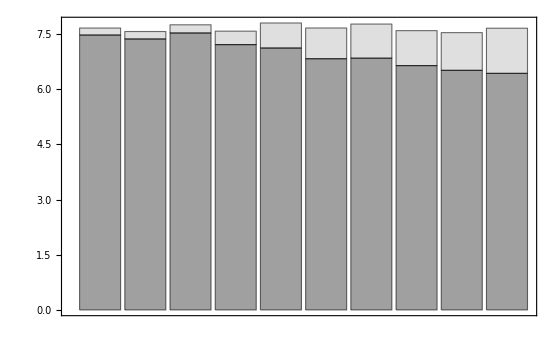

```mathematica
BarChart[histosorted⟦2,All,{9,7}⟧*100,ChartLayout->"Stacked", ChartStyle->{Directive[EdgeForm[{Thickness[Medium],Black}], Gray,Opacity[0.75]],Directive[EdgeForm[{Thickness[Medium],Black}], Gray,Opacity[0.25]]},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]]]
```

## Plot Year

#### Without tillage


```mathematica
ListPlot[ {histosorted⟦1,All,6⟧ ,histosorted⟦1,All,8⟧},Joined->True,PlotMarkers->{{-Graphics-,0.035},{-Graphics-,0.03}},PlotStyle->{Lighter[Gray],Gray},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotRange->{{0.5,10.5},{20,32}}]
```

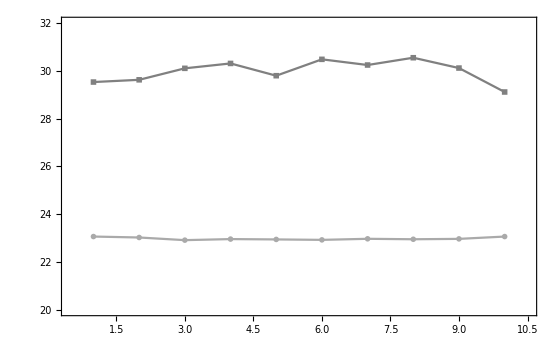

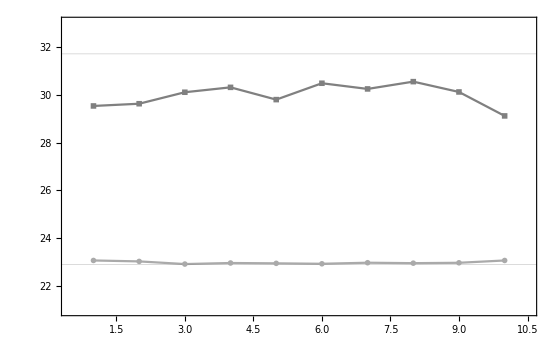

```mathematica
ListPlot[ {histosorted⟦1,All,6⟧ ,histosorted⟦1,All,8⟧},Joined->True,PlotMarkers->{{-Graphics-,0.035},{-Graphics-,0.03}},PlotStyle->{Lighter[Gray],Gray},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotRange->{{0.5,10.5},{21,33}},GridLines->{None,{{ histosorted2⟦1,2,8⟧,{Darker[Black],Thickness[0.003],Dashed}},{histosorted2⟦1,2,6⟧,{Lighter[Black],Thickness[0.003],Dashed}}}}]
```

#### With tillage

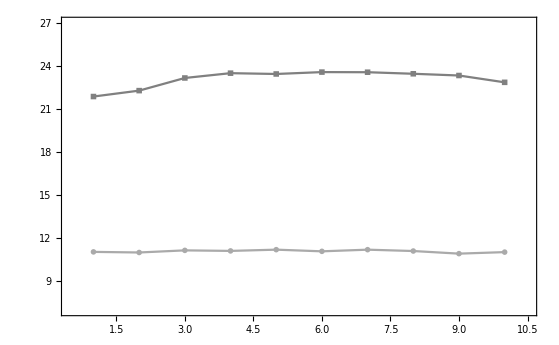

```mathematica
ListPlot[ {histosorted⟦2,All,6⟧ ,histosorted⟦2,All,8⟧},Joined->True,PlotMarkers->{{-Graphics-,0.035},{-Graphics-,0.03}},PlotStyle->{Lighter[Gray],Gray},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotRange->{{0.5,10.5},{7,27}}]
```